```mathematica
blackbody[λ_, t_]:= With[{c=3 10^8,h=6.626 10^-34,k=1.38065 10^-23},(2π h c^2)/(λ^5(Exp[(h c)/(λ k t)]-1))];
```

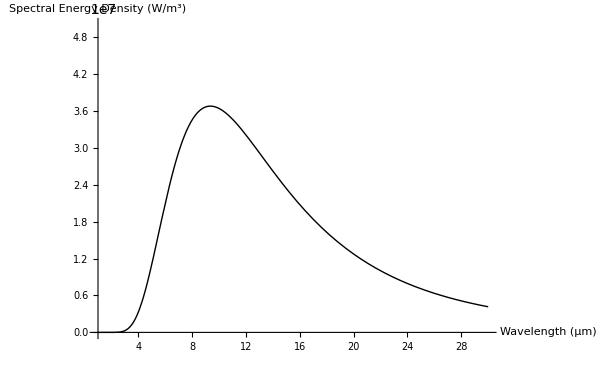

```mathematica
Plot[blackbody[x 10^-6,310],{x,1,30},PlotRange-> {0,50 10^6}, ImageSize-> 600, AxesLabel-> {"Wavelength (μm)", "Spectral Energy Density (W/m^3)"}, PlotStyle-> {Thick,Black}]
```

```mathematica
Export["~/PL.csv",Table[{λ,blackbody[λ 10^-6,310]},{λ,1,30,.2}]]
```

~/PL.csv